```mathematica
X=First[Import["Import_data.xlsx"]];
Xs=Standardize[X];
A=1/166 Transpose[Xs].Xs;
λ=Eigenvalues[A]
S=Eigenvectors[A];
For[i=1,i≤7,i++,
S[[i]]=S[[i]]/Sqrt[λ[[i]]];];
1/√λ[[1]]
Norm[S[[1]]]
```

{3.88533,1.81139,0.611559,0.333517,0.176432,0.0841622,0.0554465}

0.507325

0.507325

```mathematica
определим векторы факторных нагрузок
```

векторы нагрузок определим факторных

```mathematica
α=λ*S
```

{{-0.906443,-0.559495,-0.518735,-0.679245,-0.811176,-0.836082,-0.814343},{-0.335174,-0.668942,-0.585982,0.686748,-0.242437,0.385971,0.478349},{0.00919133,0.360839,-0.607526,0.000561338,0.223419,0.120891,-0.21829},{-0.0580478,-0.261152,-0.0295558,-0.0588703,0.472312,-0.183414,0.0298037},{-0.0619517,0.169333,-0.0218407,0.172445,-0.0201544,-0.300621,0.151416},{0.203976,-0.0605784,-0.104688,-0.0979237,-0.0611287,-0.0715973,0.0973397},{0.105347,-0.0520571,0.0108367,0.13486,-0.00746573,-0.0470602,-0.145133}}

```mathematica
Определяем количество главных факторов m,которые следует оставить в факторной модели.Критерии отбора главных факторов аналогичны критериям отбора главных компонент.
Для этого определим относительную долю дисперсии каждой компоненты
```

```mathematica
L=λ/7
```

{0.555047,0.25877,0.0873656,0.0476453,0.0252046,0.0120232,0.00792092}

```mathematica
первые две компоненты объясняют не менее "0,8" доли суммарной дисперсии, поэтому выберем их
```

```mathematica
ξ={ξ1,ξ2,ξ3,ξ4,ξ5,ξ6,ξ7};
α1=α[[1]].ξ
α2=α[[2]].ξ
```

-0.906443 ξ1-0.559495 ξ2-0.518735 ξ3-0.679245 ξ4-0.811176 ξ5-0.836082 ξ6-0.814343 ξ7

-0.335174 ξ1-0.668942 ξ2-0.585982 ξ3+0.686748 ξ4-0.242437 ξ5+0.385971 ξ6+0.478349 ξ7

```mathematica
α12=α[[1]]^2
α22=α[[2]]^2
```

{0.821638,0.313034,0.269086,0.461374,0.658007,0.699033,0.663154}

{0.112341,0.447483,0.343374,0.471623,0.0587755,0.148973,0.228818}

```mathematica
Находим значения обобщенных факторов.
```

```mathematica
Y={Xs.α[[1]],Xs.α[[2]]}
```

{{12.5628,11.4844,8.87466,10.4784,11.4007,11.0811,9.93392,8.28927,7.28845,6.98533,7.15479,5.21374,3.49781,3.22028,4.96523,3.95014,4.85309,5.26511,5.00004,5.12004,4.14249,2.92547,0.9964,-0.814761,-0.341175,-0.398236,-3.6605,-5.82472,-7.13759,-5.28742,-5.71996,-6.50879,-6.61726,-6.5605,-5.71316,-4.94883,-6.60577,-6.8882,-8.9084,-10.2548,-7.92454,-8.66037,-6.28306,-3.09919,-4.03774,-3.41059,-1.60339,-0.514094,-0.462642,-1.62083,-1.37554,-0.879127,0.00443358,-0.0580652,0.443846,1.74851,2.0141,-0.9871,-1.73069,-3.14093,-3.83097,-3.37835,-4.33475,-3.75951,-3.49601,-2.47264,-2.04908,-2.67948,-1.78775,-2.75996,-3.04156,-1.91603,-2.81863,-3.15372,-1.53841,-1.18587,-2.15422,-2.40383,-2.49929,-1.89578,-2.02685,-3.0225,-2.83333,-1.70022,-2.42513,-2.46532,-1.16654,-1.11789,-1.68895,-1.24311,-0.717468,-0.172006,-0.63553,-1.25442,-0.472373,-0.023563,-0.484044,-0.678142,1.26139,0.781674,0.627256,0.915516,0.432934,-0.0672671,0.00144727,-0.538185,-0.605297,-0.609134,-0.454375,-0.613062,-0.80756,-0.717373,-0.717529,-1.14006,-0.580253,-0.0683175,0.994944,1.04442,1.59023,1.18206,1.21954,1.02259,1.49477,2.224,2.41521,3.95367,2.85299,2.63384,1.9737,1.75485,1.19431,0.55968,0.699177,1.38022,1.37494,1.81552,2.64715,3.75267,3.8803,3.05221,2.33605,2.0872,0.675298,0.815105,0.333409,-0.288361,0.798485,0.718409,0.101837,0.162875,-0.339994,-0.789108,-1.09435,-0.811715,-0.161235,0.840987,0.119604,1.74203,3.73015,2.47446,1.92453,0.1679,-0.58415,-1.48308,-0.358149,-0.566363},{-0.869345,-1.17701,-2.45716,-1.6752,-1.36656,-1.89926,-2.35953,-2.31024,-2.87124,-2.63936,-2.52821,-3.10428,-3.37507,-3.79763,-3.08869,-3.53464,-2.7797,-1.90976,-1.66391,-1.42566,-2.00293,-2.10735,-2.94265,-3.80029,-3.50684,-3.70289,-3.10373,-4.99637,-6.30842,-5.15758,-4.62171,-4.93041,-3.97882,-3.31295,-2.27672,-1.064,-0.239905,-0.377396,-0.302814,-0.776375,0.184908,0.436954,0.118034,0.381842,1.7966,2.02431,2.15032,2.1057,2.14069,2.04533,2.45629,1.78523,2.05305,1.65248,1.93415,2.12386,1.43347,2.01744,1.47054,0.668554,0.866722,0.475287,0.265596,0.193497,0.257974,0.0104413,0.00254884,-0.0300781,0.769148,0.0651533,-0.575474,0.0665412,-0.60077,-0.770283,-0.202244,-0.271034,-0.558032,-0.386313,-0.526571,-0.141775,-0.407588,-0.879751,-0.819153,-0.374477,-0.848928,-0.844547,-0.38495,-0.471907,-0.383413,-0.359404,-0.0739883,0.609179,0.641403,0.30818,0.702483,0.738416,0.375857,0.737388,2.2437,2.02753,1.89383,1.9858,2.06959,1.81036,1.80228,0.982501,1.23973,1.17216,1.11657,0.953135,0.7652,0.924183,1.03991,0.93867,1.10181,0.908555,1.29185,1.25582,1.48662,1.05059,1.15124,1.14639,1.32971,1.3884,1.48944,1.32971,0.91057,0.932517,0.523972,0.576138,1.19482,1.06792,1.34577,1.77619,1.67263,1.70421,2.09149,2.22781,2.40638,2.30429,1.87835,1.72878,1.10617,1.36513,1.44476,1.01713,1.40311,1.23939,1.24323,1.18537,0.696899,0.464018,0.212809,0.135937,0.33253,0.498734,0.310961,0.617641,0.962843,0.587316,0.514159,0.00836755,-0.256887,-0.152234,0.400056,0.613129}}

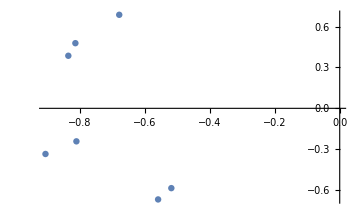

```mathematica
ListPlot[{{α[[1,1]],α[[2,1]]},{α[[1,2]],α[[2,2]]},{α[[1,3]],α[[2,3]]},{α[[1,4]],α[[2,4]]},{α[[1,5]],α[[2,5]]},{α[[1,6]],α[[2,6]]},{α[[1,7]],α[[2,7]]}},ImageSize->Medium,AxesOrigin->{0,0}]
```

```mathematica
Реализуем метод варимакс
```

метод варимакс Реализуем

```mathematica
Cp[ϕ_]:={{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}};
αpr={{-0.9064426660681882,-0.5594946802772984,-0.5187354228503089,-0.67924515476117,-0.8111761947902766,-0.8360819106791407,-0.8143426222653448},{-0.3351737513620662,-0.6689415688221616,-0.5859815518936107,0.6867478179346727,-0.2424365289370033,0.3859706890408105,0.47834893740475876}};
Vmax=0;
ϕgold=0;
ϕ=0;
```

```mathematica
While[ϕ<2π,
f=Cp[ϕ].αpr;
V=Sum[1/7 Sum[((f[[j,i]])^2-1/7 Sum[(f[[j,s]])^2,{s,1,7}])^2,{i,1,7}],{j,1,2}];
If[V≥Vmax,
Vmax=V; ϕgold=ϕ];
ϕ=ϕ+π/360;];
ϕgold
Vmax
```

(313 π)/180

0.246181

```mathematica
Таким образом лучший угол поворота 313/180 π
```

313/180 угол Таким лучший образом поворота π

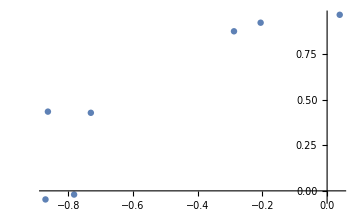

```mathematica
fpov=Cp[313/180 π].αpr;
ListPlot[{{fpov[[1,1]],fpov[[2,1]]},{fpov[[1,2]],fpov[[2,2]]},{fpov[[1,3]],fpov[[2,3]]},{fpov[[1,4]],fpov[[2,4]]},{fpov[[1,5]],fpov[[2,5]]},{fpov[[1,6]],fpov[[2,6]]},{fpov[[1,7]],fpov[[2,7]]}},ImageSize->Medium,AxesOrigin->{0,0}]
```

```mathematica
пересчитаем матрицу значений факторов и матрицу факторных нагрузок
```

и матрицу^2 значений нагрузок факторов факторных пересчитаем

```mathematica
f1=fpov[[1]].ξ
f2=fpov[[2]].ξ
Ypov={Xs.fpov[[1]],Xs.fpov[[2]]}
```

-0.863323 ξ1-0.870807 ξ2-0.782336 ξ3+0.0390115 ξ4-0.730528 ξ5-0.287925 ξ6-0.205538 ξ7

0.434342 ξ1-0.0470285 ξ2-0.0202594 ξ3+0.965129 ξ4+0.427915 ξ5+0.874703 ξ6+0.921806 ξ7

{{7.93204,6.97153,4.25545,5.9211,6.77584,6.16823,5.04926,3.96367,2.87082,2.83368,3.03054,1.28544,-0.0828678,-0.581185,1.12735,0.108912,1.27686,2.19409,2.19311,2.4492,1.36033,0.453948,-1.47258,-3.33502,-2.79742,-2.97972,-4.76638,-7.62657,-9.48151,-7.37803,-7.28111,-8.04486,-7.42288,-6.89719,-5.56146,-4.15325,-4.68058,-4.97375,-6.29698,-7.56156,-5.26929,-5.58679,-4.19871,-1.83438,-1.43978,-0.845533,0.479135,1.1894,1.25008,0.390455,0.8583,0.706069,1.50453,1.16895,1.71725,2.74578,2.42199,0.80226,-0.104843,-1.65316,-1.97883,-1.95643,-2.76205,-2.42246,-2.1956,-1.6787,-1.3956,-1.8494,-0.656724,-1.83464,-2.49522,-1.25806,-2.36168,-2.71418,-1.19711,-1.00698,-1.87729,-1.92194,-2.08962,-1.3966,-1.6804,-2.70475,-2.53142,-1.43342,-2.2748,-2.29901,-1.07711,-1.10753,-1.43227,-1.11065,-0.543424,0.328218,0.0356623,-0.630126,0.191605,0.523974,-0.0552326,0.0768003,2.5012,2.01594,1.81285,2.0767,1.80886,1.27814,1.31909,0.351515,0.493867,0.441835,0.506725,0.278972,0.00887701,0.186657,0.271191,-0.0910176,0.410085,0.617883,1.62335,1.63074,2.17178,1.57451,1.67369,1.53582,1.99192,2.53218,2.73648,3.66889,2.61168,2.47827,1.72927,1.61816,1.68836,1.16273,1.46107,2.24033,2.16099,2.48456,3.33497,4.18863,4.40628,3.76685,2.96692,2.68782,1.26956,1.55429,1.28402,0.547223,1.57074,1.39639,0.978697,0.978002,0.277805,-0.198809,-0.590704,-0.45417,0.133236,0.938303,0.308992,1.63978,3.24814,2.11711,1.68856,0.120627,-0.586264,-1.1228,0.0483257,0.0621558},{-9.78077,-9.20187,-8.1663,-8.80591,-9.26996,-9.39946,-8.8744,-7.63797,-7.28862,-6.90878,-6.95692,-5.9302,-4.85993,-4.94514,-5.73781,-5.29957,-5.44507,-5.15312,-4.79158,-4.71686,-4.39562,-3.57676,-2.73561,-1.99591,-2.14214,-2.23411,0.56038,0.852416,0.917769,0.349512,1.03132,1.3977,2.126,2.53862,2.62562,2.8937,4.66754,4.78033,6.30867,6.9704,5.92175,6.6318,4.67564,2.52702,4.17829,3.87493,2.63915,1.81207,1.7983,2.58031,2.68119,1.86047,1.39694,1.16946,0.994482,0.169694,-0.495396,2.09781,2.26866,2.75308,3.3929,2.79491,3.35137,2.88149,2.73276,1.81549,1.50034,1.93913,1.83204,2.06294,1.83199,1.44668,1.65169,1.78115,0.987193,0.682447,1.19492,1.49458,1.46874,1.28979,1.20437,1.61053,1.5135,0.98807,1.19466,1.22704,0.590618,0.495735,0.973735,0.664039,0.474263,0.541256,0.902233,1.12761,0.824564,0.520832,0.610341,0.998859,0.607682,0.811089,0.832843,0.684745,1.09483,1.28386,1.2281,1.06367,1.28818,1.2449,1.09381,1.0984,1.11248,1.15495,1.23399,1.47396,1.17581,0.669597,0.153386,0.0926291,-0.149148,-0.148002,-0.106768,0.0339626,-0.186342,-0.679644,-0.750573,-1.98467,-1.46554,-1.29029,-1.08612,-0.890488,-0.0586001,0.318999,0.40647,0.201927,0.135159,-0.165519,-0.509608,-1.22517,-1.19672,-0.660722,-0.427448,-0.347455,0.260527,0.334884,0.741485,0.904578,0.372944,0.319851,0.773405,0.689298,0.72394,0.893577,0.94549,0.68636,0.344705,-0.274923,0.124602,-0.852813,-2.0714,-1.40916,-1.05685,-0.117088,0.252024,0.980834,0.534771,0.832365}}

```mathematica
fpov[[1]]^2
fpov[[2]]^2
```

{0.745327,0.758305,0.61205,0.0015219,0.533671,0.082901,0.0422459}

{0.188653,0.00221168,0.000410443,0.931475,0.183112,0.765105,0.849726}